```mathematica
ramseyDisplacementUncert[Ω_, δ_, tf_, T_]:= 2*Ω*tf*Sinc[(δ*tf)/2]*Sin[(δ*(T+tf))/2];
Normal[Series[ramseyDisplacementUncert[Ω, δ,tf, T], {δ,0,2}]];
```

```mathematica
γ[γ0_, δ_, tc_]:= γ0*Sinc[δ*tc];
p[g_, δ_, t_,t0_,α_]:= Cos[2*Abs[γ[g, δ, t]]*Abs[α]*Sin[Arg[γ[g, δ, t, t0]] + Arg[α]]]^4
Δp[g_, δ_, t_, t0_,α_]:= Sqrt[p[γ[g, δ, t],α](1-p[γ[g, δ, t],α])]
Δω[g_,t_, δ_,α_] := FullSimplify[Δp[γ[g,δ,t],α]/Abs[D[p[g,δ, t,α],δ]]]
```

```mathematica
tCatUse = 100*10^-6;
γ0Use = 1;
tTickleUse = 100*10^-6;
```

### Compare Fisher Information for two ion (Ca-HCl) and three ion (Ca - HCl - Ca)

```mathematica
pd[γ0_,δ_,tTick_,tCat_,α_]:= Cos[2*γ[γ0, δ, tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^2;
pu[γ0_,δ_,tTick_,tCat_,α_]:= Sin[2*γ[γ0, δ, tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^2;
pdd[γ0_,δ_,tTick_,tCat_,α_]:= Cos[2*γ[γ0, δ, tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^4;
puu[γ0_,δ_,tTick_,tCat_,α_]:= Sin[2*γ[γ0,δ,tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^4;
pud[γ0_,δ_,tTick_,tCat_,α_]:= 1-Sin[2*γ[γ0,δ,tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^4-Cos[2*γ[γ0,δ,tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^4;
FITwo[γ0_,δ_,tTick_,tCat_,α_]:= (D[pd[γ0,δ,tTick,tCat, α], δ])^2/pd[γ0,δ,tTick,tCat, α]+(D[pu[γ0,δ,tTick,tCat, α], δ])^2/pu[γ0,δ,tTick,tCat, α];
FIThree[γ0_,δ_,tTick_,tCat_,α_]:= (D[pdd[γ0,δ,tTick,tCat, α], δ])^2/pdd[γ0,δ,tTick,tCat, α]+(D[puu[γ0,δ,tTick,tCat, α], δ])^2/puu[γ0,δ,tTick,tCat, α]+(D[pud[γ0,δ,tTick,tCat, α], δ])^2/pud[γ0,δ,tTick,tCat, α];


FullSimplify[FIThree[γ0,δ,tTick,tCat,α]/FITwo[γ0,δ,tTick,tCat,α]]
```

2

### Fisher Information and CR bound for Classical Ramsey Interferometry

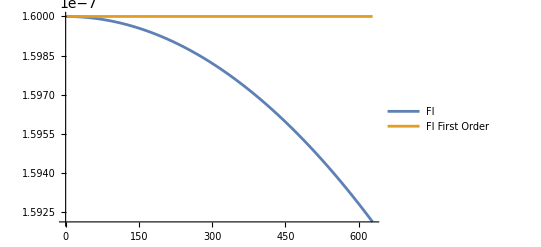

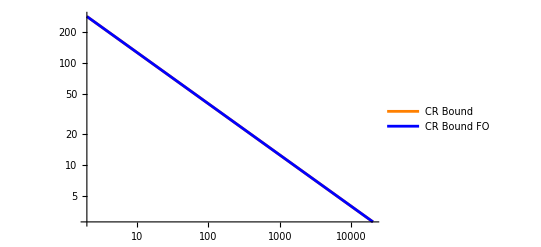

```mathematica
ramseyDisplacement[γ0_, δ_, tTick_, tAcc_]:= 2*γ0*Sinc[δ*tTick/2]*Sin[(δ*(tAcc+tTick))/2](*Exp[ⅈ*δ*(T+tf)]*);
ramseyDisplacementFO[γ0_, δ_, tTick_, tAcc_]:=Normal[Series[ramseyDisplacement[γ0, δ, tTick, tAcc], {δ,0,1}]]
FRamsey[δ_,tTick_,tAcc_,γ0_]:= 4*(Abs[D[ramseyDisplacement[γ0, δ, tTick, tAcc], δ]])^2;
FRamseyFO[δ_,tTick_,tAcc_,γ0_]:= 4*(Abs[D[ramseyDisplacementFO[γ0, δ, tTick, tAcc], δ]])^2;
FFRamseyFO =FRamseyFO[δ,tTick,tAcc,γ0]/.{tTick->tCatUse,γ0->γ0Use,tAcc->tTickleUse};
FFRamsey =FRamsey[δ,tTick,tAcc,γ0]/.{tTick->tCatUse,γ0->γ0Use,tAcc->tTickleUse};
δRamseyopt = Table[δ, {δ,1,60000}][[PositionLargest[Table[FFRamsey, {δ,1,20000}]]]][[1]];
Plot[{FFRamsey, FFRamseyFO}, {δ,0,2*π*100}, PlotLegends->{"FI", "FI First Order"}]
LogLogPlot[{1/(2*π*Sqrt[NN*FFRamsey/.{δ->δRamseyopt}]),
1/(2*π*Sqrt[NN*FFRamseyFO/.{δ->δRamseyopt}])},{NN, 2,2*10^4}, 
PlotLegends->{"CR Bound", "CR Bound FO"}, PlotStyle->{Orange, Blue, Black}]
```

## Normal Cat Interferometer SQL

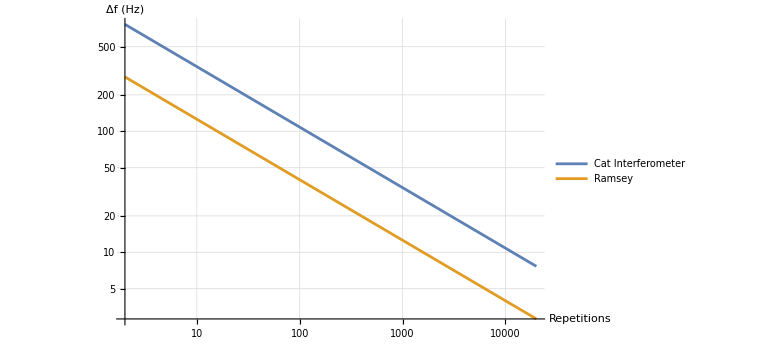

\\eric.physics.ucla.edu\groups\motion\Posters and Presentations\Josh\ATC\images\simulation_images\CRBoundunEnt.svg

```mathematica
pdd[γ0_,δ_,tTick_,tCat_,α_]:= Cos[2*γ[γ0, δ, tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^4;
puu[γ0_,δ_,tTick_,tCat_,α_]:= Sin[2*γ[γ0,δ,tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^4;
pud[γ0_,δ_,tTick_,tCat_,α_]:= 1-Sin[2*γ[γ0,δ,tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^4-Cos[2*γ[γ0,δ,tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^4;
F[g_,δ_,tTick_,tCat_,α_]:= (D[pdd[γ0,δ,tTick,tCat, α], δ])^2/pdd[γ0,δ,tTick,tCat, α]+(D[puu[γ0,δ,tTick,tCat, α], δ])^2/puu[γ0,δ,tTick,tCat, α]+(D[pud[γ0,δ,tTick,tCat, α], δ])^2/pud[γ0,δ,tTick,tCat, α];
αUse=3;
FF =F[γ0,δ,tTick,tCat,α]/.{tTick->tTickleUse, γ0->γ0Use,α->αUse,tCat->tCatUse};
FFRamsey =FRamsey[δ,tTick,tAcc,γ0]/.{tTick->tCatUse, γ0->γ0Use,tAcc->tTickleUse};
δCatopt = Table[δ, {δ,1,60000}][[PositionLargest[Table[FF, {δ,1,200}]]]][[1]];
CRBoundunEnt = LogLogPlot[{1/(2*π*Sqrt[NN*F[g,δ,tTick,tCat, α]/.{tTick->tTickleUse, γ0->γ0Use, δ->δCatopt, α->αUse, tCat->tCatUse}]),
1/(2*π*Sqrt[NN*FRamsey[δ,tTickle,tAcc, γ0]/.{tAcc->tTickleUse,γ0->γ0Use,tTickle->tCatUse, δ->δRamseyopt}])},{NN, 2,2*10^4}, 
PlotLegends->{"Cat Interferometer", "Ramsey"}, AxesLabel->{Style["Repetitions", 16], 
Style["Δf (Hz)", 16]}, GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 16], AxesStyle->Directive[Thickness[0.0025]]]
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Posters and Presentations\\Josh\\ATC\\images\\simulation_images\\CRBoundunEnt.svg", CRBoundunEnt]
```

```mathematica
fisherInfoRatioCatRamsey = (F[γ0,δ,tTick,tCat,α]/.{tTick->tTickleUse, γ0->γ0Use, δ->δCatopt, α->αUse, tCat->tCatUse})/(FRamsey[δ,tTick,tAcc, γ0]/.{tTick->tCatUse, δ->δRamseyopt, γ0->γ0Use, tAcc->tTickleUse});
N[10Log10[fisherInfoRatioCatRamsey]]
```

-8.69347

## Entangled Cat SQL

$Aborted

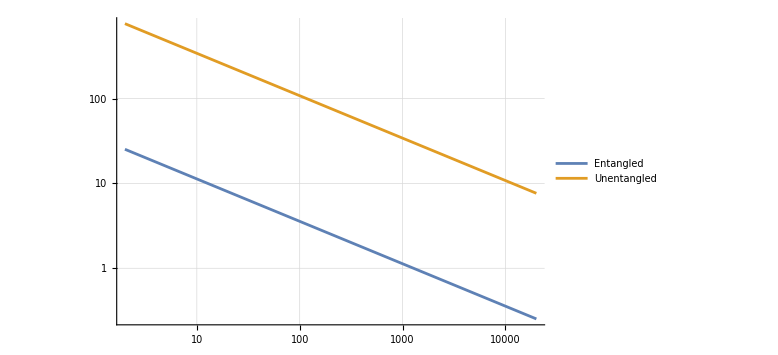
-Graphics-RepsΔf (Hz)

\\eric.physics.ucla.edu\groups\motion\Posters and Presentations\Josh\ATC\images\simulation_images\CRBoundEnt.svg

```mathematica
pddEnt[γ0_,δ_,tTick_,tCat_,α_]:= 1/2 Cos[4*γ[γ0, δ, tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^2;
puuEnt[γ0_,δ_,tTick_,tCat_,α_]:= 1/2 Cos[4*γ[γ0, δ, tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^2;
pudEnt[γ0_,δ_,tTick_,tCat_,α_]:= Sin[4*γ[γ0, δ, tCat]*α*Sin[π/2+δ*(tCat+tTick)]]^2;
FEnt[γ0_,δ_,tTick_,tCat_,α_]:= (D[pddEnt[γ0,δ,tTick,tCat, α], δ])^2/pddEnt[γ0,δ,tTick,tCat, α]+(D[puuEnt[γ0,δ,tTick,tCat, α], δ])^2/pddEnt[γ0,δ,tTick,tCat, α]+(D[pudEnt[γ0,δ,tTick,tCat, α], δ])^2/pudEnt[γ0,δ,tTick,tCat, α];
FFEnt =FEnt[γ0,δ,tTick,tCat,α]/.{tTick->tTickleUse, γ0->γ0Use, α->αUse, tCat->tCatUse};
δEntopt = Table[δ, {δ,1,200000}][[PositionLargest[Table[FFEnt, {δ,1,200000}]]]][[1]];
CRBoundEnt= Labeled[LogLogPlot[{1/(2*π*Sqrt[NN*FEnt[γ0,δ,tTick,tCat, α]/.{tTick->tTickleUse, γ0->γ0Use, δ->δEntopt, α->αUse, tCat->tCatUse}]),
1/(2*π*Sqrt[NN*F[γ0,δ,tTick,tCat, α]/.{tTick->tTickleUse, γ0->γ0Use, δ->δCatopt, α->αUse, tCat->tCatUse}])},{NN, 2,2*10^4}, 
PlotLegends->Placed[LineLegend[{Style["Entangled", 20], Style["Unentangled", 20]}, LegendMarkerSize->25], {0.75, 0.75}], GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 18]], {Style["Reps", 20], 
Style["Δf (Hz)", 20]}, {Bottom, Left}]
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Posters and Presentations\\Josh\\ATC\\images\\simulation_images\\CRBoundEnt.svg", CRBoundEnt]
```

```mathematica
fisherInfoRatioCatEnt= (FEnt[γ0,δ,tTick,tCat, α]/.{tTick->tTickleUse, γ0->γ0Use, δ->δEntopt, α->αUse, tCat->tCatUse})/(F[γ0,δ,tTick,tCat, α]/.{tTick->tTickleUse, γ0->γ0Use, δ->δCatopt, α->αUse, tCat->tCatUse});
N[20*Log10[Sqrt[fisherInfoRatioCatEnt]]]
```

29.6174

### Maximum Likelihood Estimator

```mathematica
pd[γ0_,δ_,tTick_,tCat_,α_]:= Cos[2*γ[γ0, δ, tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^2;

pdϕ[ϕ_, d_]:= (1-2*d)*Cos[ϕ]^2+d;
puϕ[ϕ_,d_]:= (1-2*d) Sin[ϕ]^2+d;
pddϕ[ϕ_, d_]:= (1-2*d)*Cos[ϕ]^4+d;
puuϕ[ϕ_, d_]:= (1-2*d)*Sin[ϕ]^4+d;
pudϕ[ϕ_, d_]:= 1-Sin[ϕ]^4-Cos[ϕ]^4;
pddEntϕ[ϕ_, d_]:= (1-4*d)*1/2 Cos[2*ϕ]^2+d;
puuEntϕ[ϕ_, d_]:= (1-4*d)*1/2 Cos[2*ϕ]^2+d;
pudEntϕ[ϕ_, d_]:= (1-4*d)*Sin[2*ϕ]^2+2*d;
```

```mathematica
LSingle[Nd_, Nu_, Pd_, Pu_, ϕ_, d_]:= Factorial[(Nd+Nu)]/(Factorial[(Nd)]*Factorial[(Nu)])*Pd[ϕ, d]^Nd*Pu[ϕ, d]^Nu;
a = FullSimplify[D[Log[LSingle[Nd, Nu, puϕ, pdϕ, ϕ, d]], ϕ]];
Solve[a==0, ϕ, Assumptions->{Nud>=0 && Nuu>=0 && Ndd>=0 && d>=0}]
```

{{ϕ→ConditionalExpression[π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[1/2 (π+2 π C[1]), C[1]∈ℤ]},{ϕ→ConditionalExpression[1/2 (ArcTan[(Nd-Nu)/((-1+2 d) (Nd+Nu)),-(2 √(-d Nd^2+d^2 Nd^2+Nd Nu-2 d Nd Nu+2 d^2 Nd Nu-d Nu^2+d^2 Nu^2))/(√(Nd^2-4 d Nd^2+4 d^2 Nd^2+2 Nd Nu-8 d Nd Nu+8 d^2 Nd Nu+Nu^2-4 d Nu^2+4 d^2 Nu^2))]+2 π C[1]), C[1]∈ℤ]},{ϕ→ConditionalExpression[1/2 (ArcTan[(Nd-Nu)/((-1+2 d) (Nd+Nu)),(2 √(-d Nd^2+d^2 Nd^2+Nd Nu-2 d Nd Nu+2 d^2 Nd Nu-d Nu^2+d^2 Nu^2))/(√(Nd^2-4 d Nd^2+4 d^2 Nd^2+2 Nd Nu-8 d Nd Nu+8 d^2 Nd Nu+Nu^2-4 d Nu^2+4 d^2 Nu^2))]+2 π C[1]), C[1]∈ℤ]}}

```mathematica
LDouble[Ndd_, Nud_, Nuu_, Pdd_, Pud_, Puu_, ϕ_, d_]:= Factorial[(Ndd+Nud+Nuu)]/(Factorial[(Ndd)]*Factorial[(Nud)]*Factorial[(Nuu)])*Pdd[ϕ,d]^Ndd*Pud[ϕ,d]^Nud*Puu[ϕ,d]^Nuu;
a = FullSimplify[D[Log[LDouble[Ndd, Nud, Nuu, pddϕ, pudϕ, puuϕ, ϕ, d]], ϕ]];
Solve[a==0, ϕ, Assumptions->{Nud>=0 && Nuu>=0 && Ndd>=0, d>=0}]
```

{{ϕ→ConditionalExpression[ArcTan[-√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,1]),-√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,1]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[-√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,1]),√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,1]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,1]),-√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,1]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,1]),√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,1]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[-√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,2]),-√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,2]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[-√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,2]),√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,2]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,2]),-√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,2]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,2]),√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,2]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[-√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,3]),-√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,3]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[-√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,3]),√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,3]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,3]),-√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,3]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,3]),√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,3]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[-√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,4]),-√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,4]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[-√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,4]),√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,4]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,4]),-√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,4]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,4]),√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,4]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[-√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,5]),-√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,5]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[-√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,5]),√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,5]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,5]),-√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,5]]+2 π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcTan[√(1-Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,5]),√Root[-d Nud+d^2 Nud+(2 d Ndd-4 d^2 Ndd+4 d Nud-6 d^2 Nud) #1+(-4 d Ndd+8 d^2 Ndd-Nud-2 d Nud+8 d^2 Nud-2 Nuu+6 d Nuu-4 d^2 Nuu) #1^2+(2 Ndd-6 d Ndd+4 d^2 Ndd+4 Nud-12 d Nud+8 d^2 Nud+6 Nuu-22 d Nuu+20 d^2 Nuu) #1^3+(-4 Ndd+16 d Ndd-16 d^2 Ndd-5 Nud+20 d Nud-20 d^2 Nud-6 Nuu+24 d Nuu-24 d^2 Nuu) #1^4+(2 Ndd-8 d Ndd+8 d^2 Ndd+2 Nud-8 d Nud+8 d^2 Nud+2 Nuu-8 d Nuu+8 d^2 Nuu) #1^5&,5]]+2 π C[1], C[1]∈ℤ]}}

```mathematica
LEnt[Ndd_, Nud_, Nuu_, PddEnt_, PudEnt_, PuuEnt_, ϕ_, d_]:= Factorial[(Ndd+Nud+Nuu)]/(Factorial[(Ndd)]*Factorial[(Nud)]*Factorial[(Nuu)])*PddEnt[ϕ, d]^Ndd*PudEnt[ϕ, d]^Nud*PuuEnt[ϕ, d]^Nuu;
a = FullSimplify[D[Log[LDouble[Ndd, Nud, Nuu, pddEntϕ, pudEntϕ, puuEntϕ, ϕ, d_]], ϕ]];
Solve[a==0, ϕ, Assumptions->{Nud>=0 && Nuu>=0 && Ndd>=0 && d>=0}]
```

{{ϕ→ConditionalExpression[(π C[1])/2, C[1]∈ℤ]},{ϕ→ConditionalExpression[1/4 (π+2 π C[1]), C[1]∈ℤ]},{ϕ→ConditionalExpression[1/4 (ArcTan[(-Ndd+Nud-Nuu)/((Ndd+Nud+Nuu) (-1+4 d_)),-((2 √(Ndd Nud+Nud Nuu-2 Ndd^2 d_-4 Ndd Nud d_-2 Nud^2 d_-4 Ndd Nuu d_-4 Nud Nuu d_-2 Nuu^2 d_+4 Ndd^2 d_^2+8 Ndd Nud d_^2+4 Nud^2 d_^2+8 Ndd Nuu d_^2+8 Nud Nuu d_^2+4 Nuu^2 d_^2))/(√(Ndd^2+2 Ndd Nud+Nud^2+2 Ndd Nuu+2 Nud Nuu+Nuu^2-8 Ndd^2 d_-16 Ndd Nud d_-8 Nud^2 d_-16 Ndd Nuu d_-16 Nud Nuu d_-8 Nuu^2 d_+16 Ndd^2 d_^2+32 Ndd Nud d_^2+16 Nud^2 d_^2+32 Ndd Nuu d_^2+32 Nud Nuu d_^2+16 Nuu^2 d_^2)))]+2 π C[1]), C[1]∈ℤ]},{ϕ→ConditionalExpression[1/4 (ArcTan[(-Ndd+Nud-Nuu)/((Ndd+Nud+Nuu) (-1+4 d_)),(2 √(Ndd Nud+Nud Nuu-2 Ndd^2 d_-4 Ndd Nud d_-2 Nud^2 d_-4 Ndd Nuu d_-4 Nud Nuu d_-2 Nuu^2 d_+4 Ndd^2 d_^2+8 Ndd Nud d_^2+4 Nud^2 d_^2+8 Ndd Nuu d_^2+8 Nud Nuu d_^2+4 Nuu^2 d_^2))/(√(Ndd^2+2 Ndd Nud+Nud^2+2 Ndd Nuu+2 Nud Nuu+Nuu^2-8 Ndd^2 d_-16 Ndd Nud d_-8 Nud^2 d_-16 Ndd Nuu d_-16 Nud Nuu d_-8 Nuu^2 d_+16 Ndd^2 d_^2+32 Ndd Nud d_^2+16 Nud^2 d_^2+32 Ndd Nuu d_^2+32 Nud Nuu d_^2+16 Nuu^2 d_^2))]+2 π C[1]), C[1]∈ℤ]}}

```mathematica
SWS
```

```mathematica
Solve[{4 N1ud Cot[2 ϕ1]-4 (N1dd+N1uu) Tan[2 ϕ1]==0, 4 N2ud Cot[2 ϕ2]-4 (N2dd+N2uu) Tan[2 ϕ2]==0}, 
{ϕ1, ϕ2},Assumptions->{N1ud>=0 && N1uu>=0 && N1dd>=0 && N2ud>=0 && N2uu>=0 && N2dd>=0}]
```

{{ϕ1→ConditionalExpression[1/2 (-ArcTan[√(N1ud/(N1dd+N1uu))]+π C[1]), C[1]∈ℤ],ϕ2→ConditionalExpression[1/2 (-ArcTan[√(N2ud/(N2dd+N2uu))]+π C[2]), C[2]∈ℤ]},{ϕ1→ConditionalExpression[1/2 (-ArcTan[√(N1ud/(N1dd+N1uu))]+π C[1]), C[1]∈ℤ],ϕ2→ConditionalExpression[1/2 (ArcTan[√(N2ud/(N2dd+N2uu))]+π C[2]), C[2]∈ℤ]},{ϕ1→ConditionalExpression[1/2 (ArcTan[√(N1ud/(N1dd+N1uu))]+π C[1]), C[1]∈ℤ],ϕ2→ConditionalExpression[1/2 (-ArcTan[√(N2ud/(N2dd+N2uu))]+π C[2]), C[2]∈ℤ]},{ϕ1→ConditionalExpression[1/2 (ArcTan[√(N1ud/(N1dd+N1uu))]+π C[1]), C[1]∈ℤ],ϕ2→ConditionalExpression[1/2 (ArcTan[√(N2ud/(N2dd+N2uu))]+π C[2]), C[2]∈ℤ]}}

### Symmetric Logarithmic Derivative

```mathematica
ClearAll[L, L00, ρ]
uu = {{1},{0}, {0}, {0}}; 
ud = {{0},{1}, {0}, {0}}; 
du = {{0},{0}, {1}, {0}}; 
dd = {{0},{0}, {0}, {1}}; 
ψ[ϕ_]:= Exp[ⅈ*θ1]*Sqrt[puuEnt[ϕ]]*uu+Exp[ⅈ*θ2]*Sqrt[1/2*pudEnt[ϕ]]*Exp[ⅈ*θ3]*ud+Sqrt[1/2*pudEnt[ϕ]]*du+Exp[ⅈ*θ4]*Sqrt[pddEnt[ϕ]]*dd
ρ[ϕ_]:=ψ[ϕ].Transpose[ψ[ϕ]];
(*L[ϕ_]:= {{L00[ϕ], L01[ϕ], L02[ϕ], L03[ϕ]},
	{L10[ϕ], L11[ϕ], L12[ϕ], L13[ϕ]},
	{L20[ϕ], L21[ϕ], L22[ϕ], L23[ϕ]},
	{L30[ϕ], L31[ϕ], L32[ϕ], L33[ϕ]}}; *)
	
L= {{L00, L01, L02, L03},
	{L10, L11, L12, L13},
	{L20, L21, L22, L23},
	{L30, L31, L32, L33}};
eqs = Thread[D[ρ[ϕ], ϕ] ==(L.ρ[ϕ]+ρ[ϕ].L)/2];
FullSimplify[ρ[ϕ]]//MatrixForm;
Solve[eqs, {L00, L01, L02, L03, 
			L10, L11, L12, L13,
			L20, L21, L22, L23,
			L30, L31, L32, L33}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{L03→-(ⅇ^(ⅈ θ2+ⅈ θ3-ⅈ θ4) L01 √pudEnt[ϕ])/(√2 √pddEnt[ϕ])-(ⅇ^(-ⅈ θ4) L02 √pudEnt[ϕ])/(√2 √pddEnt[ϕ])-(ⅇ^(ⅈ θ1-ⅈ θ4) L00 √puuEnt[ϕ])/(√pddEnt[ϕ])+(ⅇ^(ⅈ θ1-ⅈ θ4) puuEnt'[ϕ])/(√pddEnt[ϕ] √puuEnt[ϕ]),L11→-ⅇ^(-ⅈ θ2-ⅈ θ3) L12-(√2 ⅇ^(-ⅈ θ2-ⅈ θ3+ⅈ θ4) L13 √pddEnt[ϕ])/(√pudEnt[ϕ])-(√2 ⅇ^(ⅈ θ1-ⅈ θ2-ⅈ θ3) L10 √puuEnt[ϕ])/(√pudEnt[ϕ])+pudEnt'[ϕ]/pudEnt[ϕ],L22→-ⅇ^(ⅈ θ2+ⅈ θ3) L21-(√2 ⅇ^(ⅈ θ4) L23 √pddEnt[ϕ])/(√pudEnt[ϕ])-(√2 ⅇ^(ⅈ θ1) L20 √puuEnt[ϕ])/(√pudEnt[ϕ])+pudEnt'[ϕ]/pudEnt[ϕ],L30→-(ⅇ^(ⅈ θ2+ⅈ θ3-ⅈ θ4) L10 √pudEnt[ϕ])/(√2 √pddEnt[ϕ])-(ⅇ^(-ⅈ θ4) L20 √pudEnt[ϕ])/(√2 √pddEnt[ϕ])-(ⅇ^(ⅈ θ1-ⅈ θ4) L00 √puuEnt[ϕ])/(√pddEnt[ϕ])+(ⅇ^(ⅈ θ1-ⅈ θ4) puuEnt'[ϕ])/(√pddEnt[ϕ] √puuEnt[ϕ]),L31→L13+(ⅇ^(-ⅈ θ4) L12 √pudEnt[ϕ])/(√2 √pddEnt[ϕ])-(ⅇ^(-ⅈ θ4) L21 √pudEnt[ϕ])/(√2 √pddEnt[ϕ])-(ⅇ^(ⅈ θ1-ⅈ θ4) L01 √puuEnt[ϕ])/(√pddEnt[ϕ])+(ⅇ^(ⅈ θ1-ⅈ θ4) L10 √puuEnt[ϕ])/(√pddEnt[ϕ]),L32→L23-(ⅇ^(ⅈ θ2+ⅈ θ3-ⅈ θ4) L12 √pudEnt[ϕ])/(√2 √pddEnt[ϕ])+(ⅇ^(ⅈ θ2+ⅈ θ3-ⅈ θ4) L21 √pudEnt[ϕ])/(√2 √pddEnt[ϕ])-(ⅇ^(ⅈ θ1-ⅈ θ4) L02 √puuEnt[ϕ])/(√pddEnt[ϕ])+(ⅇ^(ⅈ θ1-ⅈ θ4) L20 √puuEnt[ϕ])/(√pddEnt[ϕ]),L33→-(ⅇ^(ⅈ θ2+ⅈ θ3-ⅈ θ4) L13 √pudEnt[ϕ])/(√2 √pddEnt[ϕ])-(ⅇ^(-ⅈ θ4) L23 √pudEnt[ϕ])/(√2 √pddEnt[ϕ])+(ⅇ^(ⅈ θ1+ⅈ θ2+ⅈ θ3-2 ⅈ θ4) L01 √pudEnt[ϕ] √puuEnt[ϕ])/(√2 pddEnt[ϕ])+(ⅇ^(ⅈ θ1-2 ⅈ θ4) L02 √pudEnt[ϕ] √puuEnt[ϕ])/(√2 pddEnt[ϕ])+(ⅇ^(2 ⅈ θ1-2 ⅈ θ4) L00 puuEnt[ϕ])/pddEnt[ϕ]+(ⅇ^(-2 ⅈ θ4) (ⅇ^(2 ⅈ θ4) pddEnt'[ϕ]-ⅇ^(2 ⅈ θ1) puuEnt'[ϕ]))/pddEnt[ϕ]}}

```mathematica
FullSimplify[(1-2*d)*Sin[x]^2+(1-2*d)*Cos[x]^2]
```

1-2 d